### Frictionless punch: 40x40 mesh, AG choices (m1,n1,m2,n2,ngauss)=(1,1,1,1,10)_contact stresses at element interfaces

9.47182

9.52818

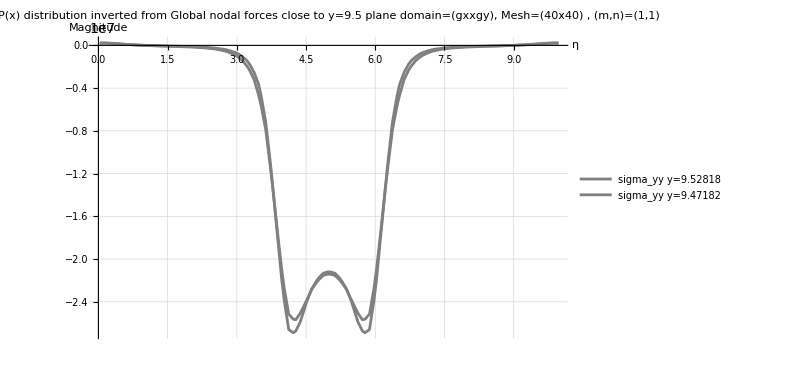

```mathematica
Clear["Global`*"]
m1=1;n1=1;m2=1;n2=1;
nx=40;
ny=40;

EE=10^9;
v=0.3;
G=EE/(2*(1+v));
Presultant=-62800000;
punchwidth=2;
AvePressure=Presultant/punchwidth;
AvePressure=1;

dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename2=StringJoin["gauss_strain_stress_deformed_disp_control_(1,1).xlsx"];
(*Read displacement data*)
{data}=Import[FileNameJoin[{dir2,filename2}]];
raw=Rest[data]; 
(*drop header row*)
gxini=raw[[All,4]];
gyini=raw[[All,5]];
gxpos=raw[[All,6]];gypos=raw[[All,7]];

ϵ11= raw[[All,9]];ϵ22=raw[[All,10]];γ12=raw[[All,11]];

σ11= raw[[All,12]];σ22=raw[[All,13]];σ12=raw[[All,14]];
σ33=raw[[All,15]];σVM=raw[[All,16]];

(*σyydata=Transpose[{gxpos,gypos,σ22}];*)
ϵxxdata=Transpose[{gxini,gyini,ϵ11}]; (*underformed gauss points*)
ϵyydata=Transpose[{gxini,gyini,ϵ22}]; (*underformed gauss points*)
γxydata=Transpose[{gxini,gyini,γ12}]; (*underformed gauss points*)

σxxdata=Transpose[{gxini,gyini,σ11/AvePressure}]; (*underformed gauss points*)
σyydata=Transpose[{gxini,gyini,σ22/AvePressure}]; (*underformed gauss points*)
σxydata=Transpose[{gxini,gyini,σ12/AvePressure}]; (*underformed gauss points*)


y0=9.5;
data=σyydata;
yVals=DeleteDuplicates[data[[All,2]]];

yBelow=Max@Select[yVals,#<y0&]
yAbove=Min@Select[yVals,#>y0&]

eps=10^-10;

curveBelow=Select[data,Abs[#[[2]]-yBelow]<eps&];
curveAbove=Select[data,Abs[#[[2]]-yAbove]<eps&];

xyBelow=curveBelow[[All,{1,3}]];
xyAbove=curveAbove[[All,{1,3}]];


ListLinePlot[{xyAbove,xyBelow},PlotRange->{All,All},
PlotStyle->{Gray},
PlotLegends->Placed[{"sigma_yy y="<>ToString[yAbove],"sigma_yy y="<>ToString[yBelow]},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces close to y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

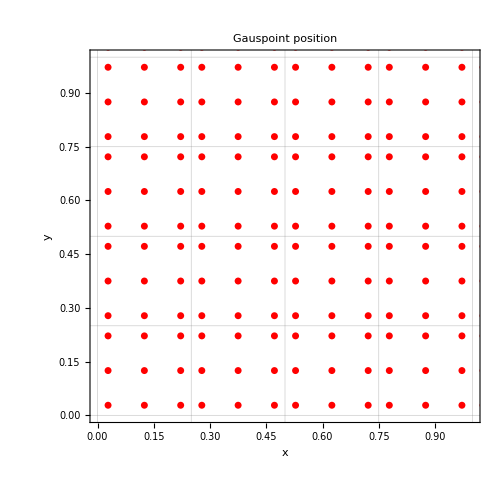

```mathematica
gaussptspos=Transpose[{gxini,gyini}];
ListPlot[gaussptspos,AspectRatio->1,PlotRange->{{0,1},{0,1}},PlotStyle->{Red,PointSize[0.01]},GridLines->{{0,0.25,0.5,0.75,1},{0,0.25,0.5,0.75,1}},PlotLabel->Style["Gauspoint position",16,Bold],Frame->True,FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->500
]
```

```mathematica
Table[i,{i,0,10,0.25}]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.,8.25,8.5,8.75,9.,9.25,9.5,9.75,10.}

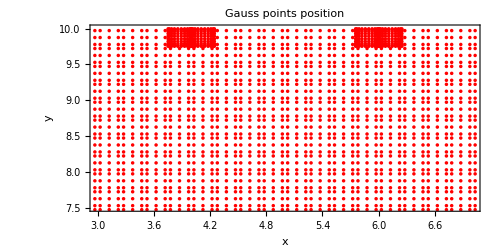

```mathematica
gaussptspos=Transpose[{gxini,gyini}];
ListPlot[gaussptspos,AspectRatio->0.5,PlotRange->{{3,7},{7.5,10}},PlotStyle->{Red,PointSize[0.005]},GridLines->{Table[i,{i,0,10,0.25}],Table[i,{i,0,10,0.25}]},PlotLabel->Style["Gauss points position",16,Bold],Frame->True,FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},ImageSize->500
]
```

#### σxx

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
σxxlist= ListPointPlot3D[σxxdata,PlotRange->{{3,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m1,n1,m2,n2)=("<>ToString[m1]<>","<>ToString[n1]<>","<>ToString[m2]<>","<>ToString[n2]<>")",16],
ImageSize->500,BoxRatios->{6,1,1}];
Show[σxxlist,zeroplane]
```

-Graphics3D-

```mathematica
σxxlist= ListPointPlot3D[σxxdata,PlotRange->{{5,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m1,n1,m2,n2)=("<>ToString[m1]<>","<>ToString[n1]<>","<>ToString[m2]<>","<>ToString[n2]<>")",16],
ImageSize->500,BoxRatios->{3,1,1}];
Show[σxxlist,zeroplane]
```

-Graphics3D-

```mathematica
Show[%30,ViewPoint->{0,∞,0}]
```

-Graphics3D-

```mathematica
Show[%32,ViewPoint->{-∞,0,0}]
```

-Graphics3D-

#### σyy

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
σyylist= ListPointPlot3D[σyydata,PlotRange->{{3,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m1,n1,m2,n2)=("<>ToString[m1]<>","<>ToString[n1]<>","<>ToString[m2]<>","<>ToString[n2]<>")",16],
ImageSize->500,BoxRatios->{6,1,1}];
Show[σyylist,zeroplane]
```

-Graphics3D-

```mathematica
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
σyylist= ListPointPlot3D[σyydata,PlotRange->{{5,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m1,n1,m2,n2)=("<>ToString[m1]<>","<>ToString[n1]<>","<>ToString[m2]<>","<>ToString[n2]<>")",16],
ImageSize->500,BoxRatios->{3,1,1}];
Show[σyylist,zeroplane]
```

-Graphics3D-

```mathematica
Show[%77,ViewPoint->{0,∞,0}]
```

-Graphics3D-

```mathematica
Show[%79,ViewPoint->{-∞,0,0}]
```

-Graphics3D-

#### σxy

```mathematica
ListContourPlot[σxydata,PlotRange->{{3,7},{9.5,10},All},(*InterpolationOrder->1,*)
Contours->20,ContourShading->True,(*set False for lines only*)ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotLegends->BarLegend[Automatic,LegendLabel->"σ_yy"],FrameLabel->{"x","y"},AspectRatio->Automatic,
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],
GridLines->{Subdivide[0,10,40],Subdivide[0,10,40]  },GridLinesStyle->Directive[Gray,Dashed,Thin],ImageSize->800]
```

-Graphics-

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
σxylist= ListPointPlot3D[σxydata,PlotRange->{{5.5,6.5},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_xy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{2,1,1}];
Show[σxylist,zeroplane]
```

-Graphics3D-

#### ϵxx

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
ϵxxlist= ListPointPlot3D[ϵxxdata,PlotRange->{{5.5,6.5},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["ϵ_xx field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{2,1,1}];
Show[ϵxxlist,zeroplane]
```

-Graphics3D-

```mathematica
ϵxxlist1= ListPointPlot3D[ϵxxdata,PlotRange->{{5.75,6},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["AG at the punch corner: ϵ_xx field ("<>ToString[nx]<>"x"<>ToString[ny]<>"), (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{1,2,1}];
Show[ϵxxlist1,zeroplane]

ϵxxlist2= ListPointPlot3D[ϵxxdata,PlotRange->{{6,6.25},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["AG at the punch corner: ϵ_xx field ("<>ToString[nx]<>"x"<>ToString[ny]<>"), (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{1,2,1}];
Show[ϵxxlist2,zeroplane]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

#### ϵyy

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
ϵyylist= ListPointPlot3D[ϵyydata,PlotRange->{{5,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["ϵ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{3,1,1}];
Show[ϵyylist,zeroplane]
```

-Graphics3D-

#### γxy

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
γxylist= ListPointPlot3D[γxydata,PlotRange->{{5.5,6.5},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["ϵ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{2,1,1}];
Show[γxylist,zeroplane]
```

-Graphics3D-

```mathematica
C:\Users\nguye\OneDrive-UCB-O365\Haden\Los Alamos NL\Work\2025_10_09_FEM static,Sparse_linalg solver\disp_control(40,40)_rigid_punch_(1,10,3)_dz=-0.1
```

```mathematica
C:\Users\nguye\OneDrive-UCB-O365\Haden\Los Alamos NL\Work\2025_10_09_FEM static,Sparse_linalg solver\disp_control(40,40)_rigid_punch_(1,10,3)_dz=-0.1
```

### welded punch: 40x40 mesh, AG choices (m1,n1,m2,n2,ngauss)=(1,1,1,1,10)

```mathematica
Clear["Global`*"]
m1=1;n1=1;m2=1;n2=1;
nx=40;
ny=40;

Presultant=-62800000;
punchwidth=2;
AvePressure=Presultant/punchwidth

dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Welded_punch_10x10geom\\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1";
filename2=StringJoin["gauss_strain_stress_deformed_disp_control_(1,1).xlsx"];
(*Read displacement data*)
{data}=Import[FileNameJoin[{dir2,filename2}]];
raw=Rest[data]; 
(*drop header row*)
gxini=raw[[All,4]];gyini=raw[[All,5]];
gxpos=raw[[All,6]];gypos=raw[[All,7]];

ϵ11= raw[[All,9]];ϵ22=raw[[All,10]];γ12=raw[[All,11]];

σ11= raw[[All,12]];σ22=raw[[All,13]];σ12=raw[[All,14]];
σ33=raw[[All,15]];σVM=raw[[All,16]];

(*σyydata=Transpose[{gxpos,gypos,σ22}];*)
ϵxxdata=Transpose[{gxini,gyini,ϵ11}]; (*underformed gauss points*)
ϵyydata=Transpose[{gxini,gyini,ϵ22}]; (*underformed gauss points*)
γxydata=Transpose[{gxini,gyini,γ12}]; (*underformed gauss points*)

σxxdata=Transpose[{gxini,gyini,σ11/AvePressure}]; (*underformed gauss points*)
σyydata=Transpose[{gxini,gyini,σ22/AvePressure}]; (*underformed gauss points*)
σxydata=Transpose[{gxini,gyini,σ12/AvePressure}]; (*underformed gauss points*)

rmax=Max[σ22]
rmin=Min[σ22]
```

-31400000

1.45219×10^7

-1.02818×10^8

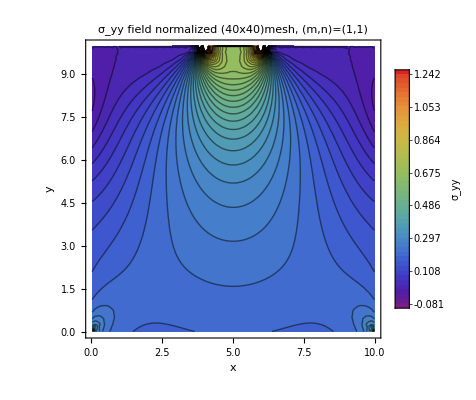

```mathematica
ListContourPlot[σyydata,PlotRange->{{0,10},{0,10},{-0.1,1.3}},(*InterpolationOrder->1,*)
Contours->50,ContourShading->True,(*set False for lines only*)ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotLegends->BarLegend[Automatic,LegendLabel->"σ_yy"],FrameLabel->{Style["x",Bold,16],Style["y",Bold,16]},AspectRatio->Automatic,
PlotLabel->Style["σ_yy field normalized \n("<>ToString[nx]<>"x"<>ToString[ny]<>") mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",Bold,16],
GridLines->{Subdivide[0,10,20],Subdivide[0,10,20]  },GridLinesStyle->Directive[Gray,Dashed,Thin]]
```

#### σxx

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
σxxlist= ListPointPlot3D[σxxdata,PlotRange->{{3,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m1,n1,m2,n2)=("<>ToString[m1]<>","<>ToString[n1]<>","<>ToString[m2]<>","<>ToString[n2]<>")",16],
ImageSize->500,BoxRatios->{6,1,1}];
Show[σxxlist,zeroplane]
```

-Graphics3D-

```mathematica
σxxlist= ListPointPlot3D[σxxdata,PlotRange->{{5,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m1,n1,m2,n2)=("<>ToString[m1]<>","<>ToString[n1]<>","<>ToString[m2]<>","<>ToString[n2]<>")",16],
ImageSize->500,BoxRatios->{3,1,1}];
Show[σxxlist,zeroplane]
```

-Graphics3D-

```mathematica
Show[%30,ViewPoint->{0,∞,0}]
```

-Graphics3D-

```mathematica
Show[%32,ViewPoint->{-∞,0,0}]
```

-Graphics3D-

#### σyy

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
σyylist= ListPointPlot3D[σyydata,PlotRange->{{3,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m1,n1,m2,n2)=("<>ToString[m1]<>","<>ToString[n1]<>","<>ToString[m2]<>","<>ToString[n2]<>")",16],
ImageSize->500,BoxRatios->{6,1,1}];
Show[σyylist,zeroplane]
```

-Graphics3D-

```mathematica
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
σyylist= ListPointPlot3D[σyydata,PlotRange->{{5,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m1,n1,m2,n2)=("<>ToString[m1]<>","<>ToString[n1]<>","<>ToString[m2]<>","<>ToString[n2]<>")",16],
ImageSize->500,BoxRatios->{3,1,1}];
Show[σyylist,zeroplane]
```

-Graphics3D-

```mathematica
Show[%77,ViewPoint->{0,∞,0}]
```

-Graphics3D-

```mathematica
Show[%79,ViewPoint->{-∞,0,0}]
```

-Graphics3D-

#### σxy

```mathematica
ListContourPlot[σxydata,PlotRange->{{3,7},{9.5,10},All},(*InterpolationOrder->1,*)
Contours->20,ContourShading->True,(*set False for lines only*)ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotLegends->BarLegend[Automatic,LegendLabel->"σ_yy"],FrameLabel->{"x","y"},AspectRatio->Automatic,
PlotLabel->Style["σ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],
GridLines->{Subdivide[0,10,40],Subdivide[0,10,40]  },GridLinesStyle->Directive[Gray,Dashed,Thin],ImageSize->800]
```

-Graphics-

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
σxylist= ListPointPlot3D[σxydata,PlotRange->{{5.5,6.5},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["σ_xy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{2,1,1}];
Show[σxylist,zeroplane]
```

-Graphics3D-

#### ϵxx

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
ϵxxlist= ListPointPlot3D[ϵxxdata,PlotRange->{{5.5,6.5},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["ϵ_xx field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{2,1,1}];
Show[ϵxxlist,zeroplane]
```

-Graphics3D-

```mathematica
ϵxxlist1= ListPointPlot3D[ϵxxdata,PlotRange->{{5.75,6},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["AG at the punch corner: ϵ_xx field ("<>ToString[nx]<>"x"<>ToString[ny]<>"), (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{1,2,1}];
Show[ϵxxlist1,zeroplane]

ϵxxlist2= ListPointPlot3D[ϵxxdata,PlotRange->{{6,6.25},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["AG at the punch corner: ϵ_xx field ("<>ToString[nx]<>"x"<>ToString[ny]<>"), (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{1,2,1}];
Show[ϵxxlist2,zeroplane]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

#### ϵyy

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
ϵyylist= ListPointPlot3D[ϵyydata,PlotRange->{{5,7},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["ϵ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{3,1,1}];
Show[ϵyylist,zeroplane]
```

-Graphics3D-

#### γxy

```mathematica
(*zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}]}];*)
zeroplane=Graphics3D[{Opacity[0.7],LightGray,Polygon[{{0,0,0},{0,10,0},{10,10,0},{10,0,0}}],(*grid lines on z=0*)Black,Thin,
Table[Line[{{x,0,0},{x,10,0}}],{x,0,10,0.25}],
Table[Line[{{0,y,0},{10,y,0}}],{y,0,10,0.25}]},Boxed->False,Lighting->"Neutral"];
γxylist= ListPointPlot3D[γxydata,PlotRange->{{5.5,6.5},{9.5,10},All},PlotStyle->{PointSize[0.006]},ColorFunction->"Rainbow",
PlotLabel->Style["ϵ_yy field ("<>ToString[nx]<>"x"<>ToString[ny]<>")mesh, (m,n)=("<>ToString[m1]<>","<>ToString[n1]<>")",16],ImageSize->500,BoxRatios->{2,1,1}];
Show[γxylist,zeroplane]
```

-Graphics3D-

```mathematica
C:\Users\nguye\OneDrive-UCB-O365\Haden\Los Alamos NL\Work\2025_10_09_FEM static,Sparse_linalg solver\disp_control(40,40)_rigid_punch_(1,10,3)_dz=-0.1
```

```mathematica
C:\Users\nguye\OneDrive-UCB-O365\Haden\Los Alamos NL\Work\2025_10_09_FEM static,Sparse_linalg solver\disp_control(40,40)_rigid_punch_(1,10,3)_dz=-0.1
```